```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->t]
```

```mathematica
T1[t_]:= t*IdentityMatrix[10]
```

```mathematica
T[t_,m_]:=T[t,m]=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;m,1;;m]]=t*IdentityMatrix[m];MAT]
```

```mathematica
Clear[leads]
```

```mathematica
leads[y_]:=leads[y]=Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_"<>ToString[y]<>"_lead_"<>ToString[x]<>"_.dat"]],{x,Range[-3,3,0.01]}]
```

```mathematica
leads[10]
```

{{{-0.452234-0.107727 ⅈ,-0.182289-0.163403 ⅈ,-0.0244543-0.145605 ⅈ,0.0481401-0.0744851 ⅈ,0.0526171+0.0032923 ⅈ,0.0226982+0.0450338 ⅈ,-0.00610083+0.037495 ⅈ,-0.0161332+0.00107833 ⅈ,-0.0112562-0.0285772 ⅈ,-0.0038863-0.0275733 ⅈ},{1},6,{1},{-0.0038863-0.0275733 ⅈ,-0.0112562-0.0285772 ⅈ,-0.0161332+0.00107833 ⅈ,-0.00610083+0.037495 ⅈ,3,-0.0244543-0.145605 ⅈ,-0.182289-0.163403 ⅈ,-0.452234-0.107727 ⅈ}},599,{1}}
 |  |  |  |

```mathematica
LEFT[ω_,m_]:=LEFT[ω,m]=leads[m][[Round[ω*100+301]]](*Module[{J=Inverse[β[ω,0.0001,1,0,m]],A:=Inverse[β[ω,0.0001,1,0,m]],T:=T1[1]},Do[J=Inverse[IdentityMatrix[m]-A.T.J.T].A,50000];J=J]*)
```

```mathematica
f1[y_,start_,stop_]:= Table[{x,y},{x,start,stop}]
```

```mathematica
s[xstart_,xstop_,ystart_,ystop_]:=Module[{J=f1[ystart,xstart,xstop]},Do[J=Join[f1[y,xstart,xstop],J],{y,ystart+1,ystop}];J=J]
```

```mathematica
Clear[dist]
```

```mathematica
dist[concentration_]:=dist[concentration]=Table[SortBy[Join[RandomSample[Join[s[1,25,1,50],s[26,50,1,25]],concentration],RandomSample[Join[(*s[1,25,13,50],*)s[26,50,26,50]],50-concentration]],First],10000]
```

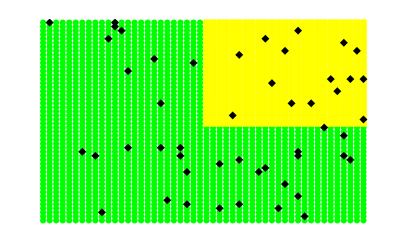

```mathematica
ListPlot[{Join[s[1,25,1,50],s[26,50,1,25]],Join[(*s[1,25,13,50],*)s[26,50,25,50]],dist[35][[30]]},PlotMarkers->Automatic,PlotStyle->{Green,Yellow,Black},Axes->False]
```

```mathematica
TLD[t_]:=Module[{sizeoflead=10},Module[{mat=RandomInteger[0,{50,50}]},ReplacePart[mat,Table[{a,a},{a,41,50}]->t]]]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ,50]]
```

```mathematica
SLLEAD[ω_,m_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;m,1;;m]]=LEFT[ω,m];MAT]
```

```mathematica
SRLEAD[ω_,m_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[41;;50,41;;50]]=LEFT[ω,m];MAT]
```

```mathematica
CA[ω_,δ_,t_,ϵ_,ϵ1_,concentration_,number_]:= Module[{sizeoflead=10},
recurs=Module[{J1= device1[ω]},
Do[
J1=Inverse[IdentityMatrix[50]-Inverse[Module[{J=β[ω,δ,t,ϵ,50]},Do[J=Module[{m=unitcell},If[dist[concentration][[number]][[loc1,1]]==m,ReplacePart[J,{{dist[concentration][[number]][[loc1,2]],dist[concentration][[number]][[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,50}];J]].T[1,50].J1.T[1,50]].Inverse[Module[{J=β[ω,δ,t,ϵ,50]},Do[J=Module[{m=unitcell},If[dist[concentration][[number]][[loc1,1]]==m,ReplacePart[J,{{dist[concentration][[number]][[loc1,2]],dist[concentration][[number]][[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,50}];J]],{unitcell,50}];J1=J1];ir=Inverse[IdentityMatrix[50]-SRLEAD[ω,sizeoflead].TLD[1].recurs.TLD[1]].SRLEAD[ω,sizeoflead];il=Inverse[IdentityMatrix[50]-recurs.TLD[1].SRLEAD[ω,sizeoflead].TLD[1]].recurs;
gdd1= il-ConjugateTranspose[il];
grr1= ir-ConjugateTranspose[ir];
Gnonlocalrl=ir.TLD[1].recurs;
GNON1= Gnonlocalrl-ConjugateTranspose[Gnonlocalrl];TRA=Abs[Tr[gdd1.TLD[1].grr1.TLD[1]-TLD[1].GNON1.TLD[1].GNON1]];TRA]
```

```mathematica
Mean[ParallelTable[CA[1,0.0001,1,0,1,30,n],{n,800}]]
```

2.96437

```mathematica
Monitor[Table[Export["/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/1_4th/50_ϵ1_conc_"<>ToString[conc]<>"_.dat",Table[{ω,Mean[ParallelTable[CA[ω,0.0001,1,0,1,conc,n],{n,800}]]},{ω,Range[-3,3,0.01]}]],{conc,5,45,5}],conc]
```

{/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/1_4th/50_ϵ1_conc_5_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/1_4th/50_ϵ1_conc_10_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/1_4th/50_ϵ1_conc_15_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/1_4th/50_ϵ1_conc_20_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/1_4th/50_ϵ1_conc_25_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/1_4th/50_ϵ1_conc_30_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/1_4th/50_ϵ1_conc_35_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/1_4th/50_ϵ1_conc_40_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/1_4th/50_ϵ1_conc_45_.dat}

```mathematica
transmission = Table[{x,Import["/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/1_4th/50_ϵ1_conc_"<>ToString[x]<>"_.dat"]},{x,Range[5,45,5]}]
```

{{5,{{-3.,1.36294},{-2.99,1.52606},{-2.98,1.52672},{-2.97,1.39355},{-2.96,1.24439},{-2.95,1.3429},{-2.94,1.45868},{-2.93,1.4042},{-2.92,1.22361},{-2.91,1.20568},{-2.9,0.999171},{-2.89,1.31291},{-2.88,1.13151},576,{2.89,0.973154},{2.9,0.987954},{2.91,1.02794},{2.92,0.947192},{2.93,0.896294},{2.94,0.887256},{2.95,0.893622},{2.96,0.886737},{2.97,0.991948},{2.98,1.04477},{2.99,1.03297},{3.,0.961194}}},7,{45,{1}}}
 |  |  |  |

```mathematica
input =Monitor[Table[ParallelTable[{ω,CA[ω,0.0001,1,0,1,35,n]},{ω,Range[-3,3,0.01]}],{n,30}],n]
```

{{{-3.,2.03176},{-2.99,1.80338},{-2.98,1.96779},{-2.97,1.81513},{-2.96,1.06029},{-2.95,1.034},589,{2.95,0.843715},{2.96,0.912741},{2.97,1.78111},{2.98,1.87152},{2.99,0.945751},{3.,1.39931}},28,{1}}
 |  |  |  |

```mathematica
Dimensions[transmission]
```

{9,2}

```mathematica
Clear[misfit]
```

```mathematica
misfit[x_,y_,n_]:=misfit[x,y,n]=Module[{m5=input[[n]]},
ρ1=Table[{transmission[[con,1]],Module[{B1=Transpose[{m5[[1;;601]][[;;,1]],(m5[[1;;601,2]]-transmission[[con,2]][[1;;601,;;]][[;;,2]])^2}]},NIntegrate[Interpolation[B1][ω],{ω,y,x}]]},{con,9}];lista=ρ1;
{lista,lista[[Position[lista,Min[lista]][[1,1]]]]}]
```

```mathematica
Monitor[Table[Monitor[Mean[Table[Mean[ParallelTable[misfit[x,y,n][[2]][[1]],{y,Range[-0.5,x,0.05]}]],{x,Range[-0.3,3,0.1]}]],x],{n,30}],n]
```

{25727670247827391148971354536577/597554629065694587196101882690,12307935389826626204673938558063/298777314532847293598050941345,4962664754073096225304525305445/119510925813138917439220376538,11454484212469567153149524956967/298777314532847293598050941345,1114630617876114460517533733/35809590044087888008395870,3939467381729844150076950026054/99592438177615764532683647115,25355611543319114912666108262263/597554629065694587196101882690,421300142497521349619509157299/10864629619376265221747306958,49371027273848154468514951601/2011968448032641707730982770,17761267507818359320137430996129/597554629065694587196101882690,1923216974989851228500190661867/66394958785077176355122431410,66432229943808902388377067119/2586816576041967909939834990,672592752736040209005988285079/18107716032293775369578844930,18282686717701563592441827522589/597554629065694587196101882690,25150635272944178160980075379629/597554629065694587196101882690,25259740309455728750223656019259/597554629065694587196101882690,10519654840346167235475080703377/298777314532847293598050941345,16913313346221161849951734129/729614931704144795111235510,19706096888450942070409454226491/597554629065694587196101882690,22655672247597308345389973586323/597554629065694587196101882690,3493651181593345804649127893473/85364947009384941028014554670,18681299420245838425735255995253/597554629065694587196101882690,59421045555301146951169440419/2510733735570145324353369255,1013090241784756078387528456951/33197479392538588177561215705,20102864476283205947080580453707/597554629065694587196101882690,204427054699738349741902593767/6035905344097925123192948310,11879039198011857507458582168953/298777314532847293598050941345,12814147648841713131817786272127/298777314532847293598050941345,7257490996730698732742466876386/298777314532847293598050941345,106814192319873822921338902849/2943618862392584173379812230}

```mathematica
Mean[Abs[N[%107]-35]/35]
```

0.157454

```mathematica
Mean[Flatten[%77]]
```

17125/408

```mathematica
N[17125/408]
```

41.973

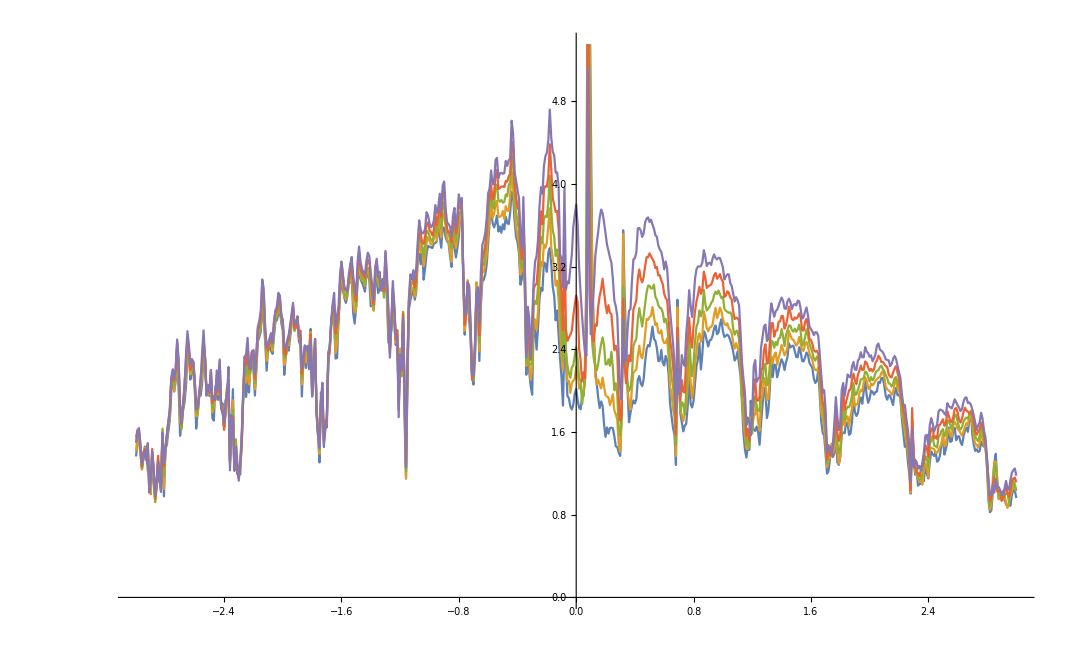

```mathematica
ListLinePlot[Table[transmission[[con,2]],{con,1,9,2}]]
```